# 1D LLS with t0

```mathematica
Cc[N_,k_]:= N!/((k-3)!(N-k)!)
```

```mathematica
Pd[x_,t0_]:= (x-t0)/(1-t0)
```

```mathematica
pd[x_,t0_]:= D[Pd[x,t0],x]
```

```mathematica
phi[x2_,xk_,N_,k_, t0_] := Cc[N,k] *Pd[x2,t0]*(Pd[xk,t0] - Pd[x2,t0])^(k - 3)*(1 - Pd[xk,t0])^(N - k)*pd[x2,t0]*pd[xk,t0]
```

```mathematica
Refine[∫_t0^1 ∫_(2xk/3)^xk phi[x2,xk,N,k]ⅆx2ⅆxk, {Element[N,Integers] &&  N>3,Element[k,Integers] && k>=2 && N>=k, Element[t0,Reals] && 1>t0>0}]
```

(3^(1-k) (-1+2 k) (Beta[1,k,1-k+N]-Beta[t0,k,1-k+N]) N!)/(Gamma[k] Gamma[1-k+N])

```mathematica
pi[k_,N_, t0_] :=(3^(1-k) (-1+2 k) (Beta[1,k,1-k+N]-Beta[t0,k,1-k+N]) N!)/(Gamma[k] Gamma[1-k+N])
```

```mathematica
Simplify[pi[3,10, t0]]
```

5/9-200 Beta[t0,3,8]

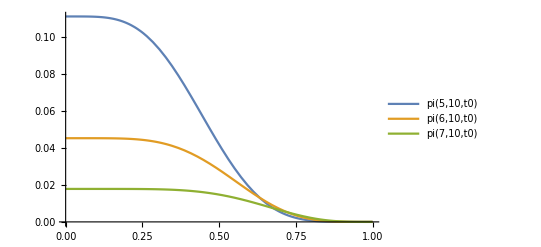

```mathematica
Plot[{pi[5,10,t0], pi[6,10,t0], pi[7,10,t0]},{t0,0,1}, PlotLegends->"Expressions"]
```

```mathematica
Ck[N_,k_] := 2(N-k)/((N-1)(N-2))
```

```mathematica
tempPh=FullSimplify[Refine[∑_(k=2)^N Ck[N,k]*pi[k,N, t0], {Element[N,Integers]&& N>0,Element[t0,Reals] && 1>t0>0}]]
```

∑_(k=2)^N (2 3^(1-k) (-1+2 k) (-k+N) (Beta[1,k,1-k+N]-Beta[t0,k,1-k+N]) N!)/((-2+N) (-1+N) Gamma[k] Gamma[1-k+N])

```mathematica
Ph[N_,t0_] := ∑_(k=2)^N (2 3^(1-k) (-1+2 k) (-k+N) (Beta[1,k,1-k+N]-Beta[t0,k,1-k+N]) N!)/((-2+N) (-1+N) Gamma[k] Gamma[1-k+N])
```

```mathematica
N[Ph[10,0]]
```

0.395858

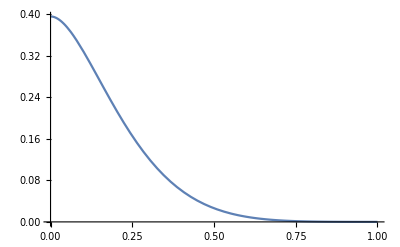

```mathematica
Plot[ Function[t0, Ph[10,t0]][x],{x,0,1}]
```